# Vacuum Stability

## Basic Setup

```mathematica
ClearAll["Global`*"];
```

```mathematica
SMparam={g-> 0.65,gY-> 0.36,yt-> 0.9945,mh-> 125.,v-> 174.,Q-> 150};(*SM parameters*)
```

```mathematica
V0[λ_,A_,μH_,μS_,h_,S_]:=1/4 λ h^4-1/2 μH^2 h^2+1/2 μS^2 S^2-1/2 A S (h^2-2 v^2);(*This convention keeps the vev of S at vacuum to be 0. The v here is the physical vev at 1-loop level, which is 174 GeV. Note that the tree-level potential may not have a vev here.*)
mW[h_]:=1/4 g^2 h^2;
mZ[h_]:=1/4(g^2+gY^2)h^2;
mt[h_]:=1/2 yt^2 h^2;
VCW[λ_,A_,μH_,μS_,h_]:=1/(64 π^2)(6 mW[h]^2(Log[mW[h]/Q^2]-5/6)+3 mZ[h]^2(Log[mZ[h]/Q^2]-5/6)-12 mt[h]^2(Log[mt[h]/Q^2]-3/2));
V0Tpre[λ_,A_,μH_,μS_,h_,S_]:=V0[λ,A,μH,μS,h,S]+VCW[λ,A,μH,μS,h];(*Effective Potential at T=0.*)
```

## Parametrization up to 1-loop level: fix the zero temperature vev and Higgs mass

We have 4 bare parameters: λ, A, μ_H, and μ_S. These 4 bare parameters are transferred into 4 physical, observable parameters: m_H=125. GeV, m_S, v=174. GeV, sinθ. We need 4 equations to get them. For the masses and the mixing angle, the equation is just given by the definition. For the vev, the equation is given by the fact that the 1st order derivative of the 1-loop level potential at this point is 0.

```mathematica
MassMatrix=D[V0Tpre[λ,A,μH,μS,h,S],{{h,S},2}]/.{h->√2 v,S->0}/.SMparam//N//Simplify;
MassMatrix//MatrixForm
mh‵renorm=Eigensystem[MassMatrix]⟦1,2⟧
mS‵renorm=Eigensystem[MassMatrix]⟦1,1⟧
tanθ‵renorm=Eigensystem[MassMatrix]⟦2,1,1⟧(*tan θ*)
derivative=D[V0Tpre[λ,A,μH,μS,h,S],h]/.{h->√2 v,S->0}/.SMparam
```

(46.0398+181656. λ-1. μH^2 | -246.073 A
-246.073 A | μS^2)

0.5 (46.0398+181656. λ-1. μH^2+1. μS^2+1. √((-46.0398-181656. λ+1. μH^2-μS^2)^2-4 (-60552. A^2+46.0398 μS^2+181656. λ μS^2-1. μH^2 μS^2)))

-0.5 (-46.0398-181656. λ+1. μH^2-1. μS^2+1. √((-46.0398-181656. λ+1. μH^2-μS^2)^2-4 (-60552. A^2+46.0398 μS^2+181656. λ μS^2-1. μH^2 μS^2)))

1/A 0.00203192 (-46.0398-181656. λ+1. μH^2+1. μS^2+1. √((-46.0398-181656. λ+1. μH^2-μS^2)^2-4 (-60552. A^2+46.0398 μS^2+181656. λ μS^2-1. μH^2 μS^2)))

180566.+1.49002×10^7 λ-246.073 μH^2

## One benchmark as example: m_S=5 GeV, sin θ=0.17

Take an example here.

```mathematica
{λ‵renorm,A‵renorm,μH‵renorm,μS‵renorm}={λ,A,μH,μS}/.NSolve[{mh‵renorm2==125^2,mS‵renorm2==5^2,tanθ‵renorm2==√(0.17^2/(1-0.17^2)),derivative==0},{λ,A,μH,μS},PositiveReals]//Flatten
```

{0.130978,10.6204,93.0846,21.8138}

Plug back to the expression. Now this is the effective potential for this benchmark.

```mathematica
V0T‵BPeg[h_,S_]=V0Tpre[λ‵renorm,A‵renorm,μH‵renorm,μS‵renorm,h,S]/.SMparam
```

-4332.37 h^2+0.0327444 h^4-5.3102 (-60552.+h^2) S+237.92 S^2+(0.0669398 h^4 (-5/6+Log[4.69444×10^-6 h^2])+0.0571527 h^4 (-5/6+Log[6.13444×10^-6 h^2])-2.93454 h^4 (-3/2+Log[0.0000219785 h^2]))/(64 π^2)

```mathematica
Plot3D[{V0T‵BPeg[h,S]},{h,0,5000},{S,0,100000}]
```

-Graphics3D-

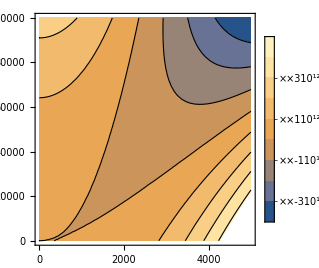

```mathematica
ContourPlot[V0T‵BPeg[h,S],{h,0,5000},{S,0,100000},PlotLegends->Automatic]
```

Confirm whether the observable is really fixed.

```mathematica
{hvev,Svev}={h,S}/.FindRoot[D[V0T‵BPeg[h,S],h]==0&&D[V0T‵BPeg[h,S],S]==0,{h,246},{S,0}](*Location of vevs*)
```

{246.073,2.14327×10^-11}

```mathematica
FindMinimum[V0T‵BPeg[h,S],{{h,246},{S,0}}](*Other method to check the vev*)
```

{-1.2301×10^8,{h→246.073,S→2.24301×10^-11}}

```mathematica
Svevpath[h_]:=(A‵renorm)/(2(μS‵renorm)^2)(h^2-hvev^2)
```

```mathematica
M=D[V0T‵BPeg[h,S],{{h,S},2}]/.{h->hvev,S->Svev}//Simplify;
M//MatrixForm
Sqrt[Eigenvalues[M]]
(*Check the scalar masses*)
```

(15174.2 | -2613.4
-2613.4 | 475.84)

{125.,5.}

Export this potential.

```mathematica
DumpSave[NotebookDirectory[]<>"output/V0T_BPeg.m",V0T‵BPeg]
```

{V0T‵BPeg}

### Check the bounce solution from simplebounce code

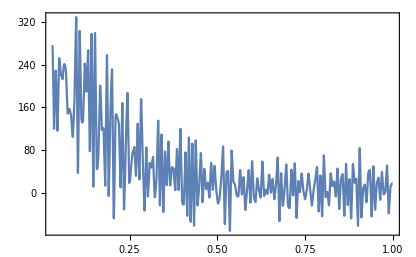

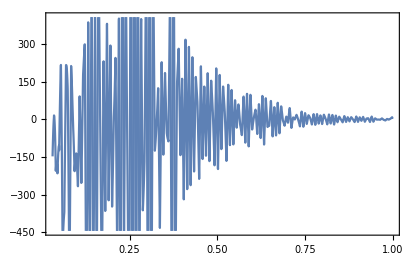

```mathematica
pathdata={0.01*#1,100*#2,100*#3}& @@@Import[NotebookDirectory[]<>"output/BPeg.csv","Data"][[2;;]];
Spath[h_]:=Interpolation[pathdata[[All,{2,3}]]][h];
hevolve[r_]:=Interpolation[pathdata[[All,{1,2}]]][r];
Sevolve[r_]:=Interpolation[pathdata[[All,{1,3}]]][r];
hpath[S_]:=Interpolation[pathdata[[All,{3,2}]]][S];
dV0Tdh[h_,S_]:=D[V0T‵BPeg[ϕ,S],ϕ]/.{ϕ->h};
dV0TdS[h_,S_]:=D[V0T‵BPeg[h,ϕ],ϕ]/.{ϕ->S};
eqh[r_]:=hevolve''[r]+3/r hevolve'[r]-dV0Tdh[hevolve[r],Sevolve[r]];
eqs[r_]:=Sevolve''[r]+3/r Sevolve'[r]-dV0TdS[hevolve[r],Sevolve[r]];
Plot[eqh[r],{r,.03,1}]
Plot[eqs[r],{r,.03,1}]
```

## Try several different benchmarks

This section try several benchmarks in the model, especially for the points at the corner of the m_S-sinθ plane.

```mathematica
params[mS_,sinθ_]:=(
NSolve[{mh‵renorm2==125^2,mS‵renorm2==mS^2,tanθ‵renorm2==√(sinθ^2/(1-sinθ^2)),derivative==0},{λ,A,μH,μS},PositiveReals]//Flatten
)
```

```mathematica
{λ,A,μH,μS}/.params[2,0.3]
{λ,A,μH,μS}/.params[15,0.3]
{λ,A,μH,μS}/.params[2,0.01]
{λ,A,μH,μS}/.params[15,0.01]
```

{0.123091,18.1671,90.4833,37.5485}

{0.123256,17.9101,90.5382,40.1373}

{0.134687,0.634779,94.2835,2.35841}

{0.134688,0.625799,94.2836,15.0512}

```mathematica
V0T‵BP1[h_,S_]=V0Tpre[λ,A,μH,μS,h,S]/.SMparam/.params[2,0.3];
V0T‵BP2[h_,S_]=V0Tpre[λ,A,μH,μS,h,S]/.SMparam/.params[15,0.3];
V0T‵BP3[h_,S_]=V0Tpre[λ,A,μH,μS,h,S]/.SMparam/.params[2,0.01];
V0T‵BP4[h_,S_]=V0Tpre[λ,A,μH,μS,h,S]/.SMparam/.params[15,0.01];
Svevpath‵BP1[h_]:=A/(2 μS^2)(h^2-246.073^2)/.params[2,0.3];
Svevpath‵BP2[h_]:=A/(2 μS^2)(h^2-246.073^2)/.params[15,0.3];
Svevpath‵BP3[h_]:=A/(2 μS^2)(h^2-246.073^2)/.params[2,0.01];
Svevpath‵BP4[h_]:=A/(2 μS^2)(h^2-246.073^2)/.params[15,0.01];
```

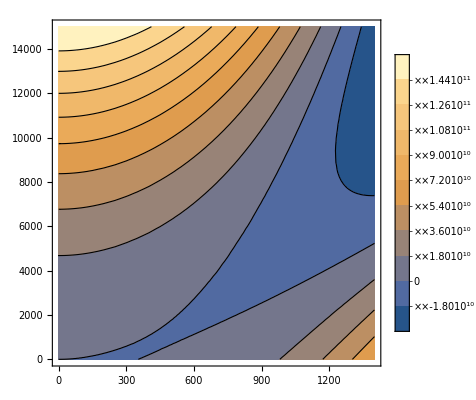

```mathematica
ContourPlot[V0T‵BP1[h,S],{h,0,1400},{S,0,15000},PlotLegends->Automatic,Contours->10]
```

```mathematica
Plot3D[V0T‵BP1[h,S],{h,200,350},{S,0,200}]
```

-Graphics3D-

```mathematica
FindRoot[D[V0T‵BP1[h,S],h]==0&&D[V0T‵BP1[h,S],S]==0,{h,246},{S,0}]
FindRoot[D[V0T‵BP2[h,S],h]==0&&D[V0T‵BP1[h,S],S]==0,{h,246},{S,0}]
FindRoot[D[V0T‵BP3[h,S],h]==0&&D[V0T‵BP1[h,S],S]==0,{h,246},{S,0}]
FindRoot[D[V0T‵BP4[h,S],h]==0&&D[V0T‵BP1[h,S],S]==0,{h,246},{S,0}]
```

{h→246.073,S→-1.22649×10^-11}

{h→246.073,S→3.75729×10^-11}

{h→246.073,S→3.00702×10^-13}

{h→246.073,S→-7.69853×10^-13}

```mathematica
Table[Svevpath‵BP1[h],{h,{300,500,1000,2000}}]
```

{189.727,1220.57,6052.63,25380.9}

```mathematica
Table[Svevpath‵BP2[h],{h,{300,500,1000,2000}}]
```

{163.693,1053.08,5222.11,21898.2}

```mathematica
Table[Svevpath‵BP3[h],{h,{1000,3000,5000,8000,10000}}]
```

{53607.7,510111.,1.42312×10^6,3.64857×10^6,5.70284×10^6}

```mathematica
Table[Svevpath‵BP4[h],{h,{20000,25000,30000}}]
```

{552401.,863173.,1.24301×10^6}

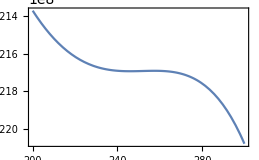

```mathematica
Plot[V0T‵BP1[h,Svevpath‵BP1[h]],{h,200,300}]
```

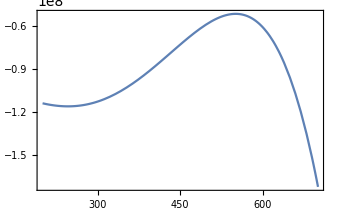

```mathematica
Plot[V0T‵BP2[h,Svevpath‵BP2[h]],{h,200,700}]
```

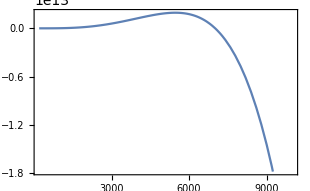

```mathematica
Plot[V0T‵BP3[h,Svevpath‵BP3[h]],{h,200,10000}]
```

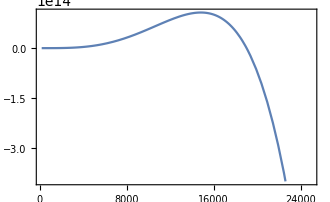

```mathematica
Plot[V0T‵BP4[h,Svevpath‵BP4[h]],{h,200,25000}]
```

```mathematica
FindRoot[D[V0T‵BP4[h,S],h]==0&&D[V0T‵BP1[h,S],S]==0,{h,246},{S,0}]
```

{h→246.073,S→-7.69853×10^-13}

### Summary after running 4 benchmarks in simplebounce

The best result comes from the BP2. It quickly gives me a beautiful solution, with large bounce action, and trajectory along the valley of the potential.
The other benchmarks have their own problem each.
BP1: The bump is too low. I tried many different initial condition in simple bounce, it always diverge. I doubt that with such low bump the potential will behave like pure -ϕ^4. In this case the bounce does not exist. But the pseudo-bounce solution makes us safe.
BP3&4: Seems numerical error happens. The field value is too large compare to the vev. However, increasing the digit or using larger unit do not solve the problem.